```mathematica
<<ComputationalGeometry`
Needs["TetGenLink`"];
Clear[s];
BordaS[sigma_,sigmaP_] := (n=Length[sigma];Sum[(n-sigma[[i]])*(n-sigmaP[[i]]),{i,1,n}]);
Mat[S_,n_]:=(P=Permutations[Range[1,n],{n}];Table[Table[S[sigma,sigmaP],{sigmaP,P}],{sigma,P}]);
dot[A_,B_]:=(k=Length[A];Sum[A[[i]]*B[[i]],{i,1,n}]);
R[S_,n_]:=(M = Mat[S,n];Print[MatrixForm[M]];Print[Eigenvalues[M]];EV=Eigenvectors[M]; Print[MatrixForm[Transpose[EV]]];MatrixRank[M]);
```

```mathematica
R[BordaS,3]
```

(5 | 4 | 4 | 2 | 2 | 1
4 | 5 | 2 | 4 | 1 | 2
4 | 2 | 5 | 1 | 4 | 2
2 | 4 | 1 | 5 | 2 | 4
2 | 1 | 4 | 2 | 5 | 4
1 | 2 | 2 | 4 | 4 | 5)

{18,6,6,0,0,0}

(1 | -1 | 0 | 3 | 2 | 2
1 | 0 | -1 | -2 | -1 | -2
1 | -1 | 1 | -2 | -2 | -1
1 | 1 | -1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0
1 | 1 | 0 | 1 | 0 | 0)

3

```mathematica
M = Mat[BordaS,3]
```

{{5,4,4,2,2,1},{4,5,2,4,1,2},{4,2,5,1,4,2},{2,4,1,5,2,4},{2,1,4,2,5,4},{1,2,2,4,4,5}}

```mathematica
M.Transpose[M]==Transpose[M].M
```

True

```mathematica
|
```

```mathematica
{U,DD,V} = SingularValueDecomposition[M]
```

{{{1/(√6),-1/2,-1/(2 √3),1/(√2),0,0},{1/(√6),0,-1/(√3),-(√2)/3,1/(3 √2),-(√2)/3},{1/(√6),-1/2,1/(2 √3),-(√2)/3,-(√2)/3,1/(3 √2)},{1/(√6),1/2,-1/(2 √3),0,0,1/(√2)},{1/(√6),0,1/(√3),0,1/(√2),0},{1/(√6),1/2,1/(2 √3),1/(3 √2),-(√2)/3,-(√2)/3}},{{18,0,0,0,0,0},{0,6,0,0,0,0},{0,0,6,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{1/(√6),-1/2,-1/(2 √3),1/(√2),0,0},{1/(√6),0,-1/(√3),-(√2)/3,1/(3 √2),-(√2)/3},{1/(√6),-1/2,1/(2 √3),-(√2)/3,-(√2)/3,1/(3 √2)},{1/(√6),1/2,-1/(2 √3),0,0,1/(√2)},{1/(√6),0,1/(√3),0,1/(√2),0},{1/(√6),1/2,1/(2 √3),1/(3 √2),-(√2)/3,-(√2)/3}}}

```mathematica
EMB = U.MatrixPower[DD,1/2]
```

{{√3,-√(3/2),-1/(√2),0,0,0},{√3,0,-√2,0,0,0},{√3,-√(3/2),1/(√2),0,0,0},{√3,√(3/2),-1/(√2),0,0,0},{√3,0,√2,0,0,0},{√3,√(3/2),1/(√2),0,0,0}}

```mathematica
EV=Eigenvectors[Mat[BordaS,3]]
```

{{1,1,1,1,1,1},{-1,0,-1,1,0,1},{0,-1,1,-1,1,0},{3,-2,-2,0,0,1},{2,-1,-2,0,1,0},{2,-2,-1,1,0,0}}

```mathematica
EMB3 = {{0.6134,1.2743},{1.4102,0.106},{-0.7969,1.1683},{0.7969,-1.1683},{-1.4102,-0.106},{-0.6134,-1.2743}};
```

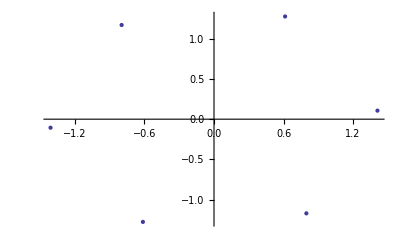

```mathematica
ListPlot[EMB3[[ConvexHull[EMB3]]]]
```

```mathematica
Mat[BordaS,4]
```

{{14,13,13,11,11,10,13,12,11,8,9,7,11,9,10,7,6,5,8,7,7,5,5,4},{13,14,11,13,10,11,12,13,8,11,7,9,9,11,7,10,5,6,7,8,5,7,4,5},{13,11,14,10,13,11,11,9,13,7,12,8,10,6,11,5,9,7,7,5,8,4,7,5},{11,13,10,14,11,13,9,11,7,13,8,12,6,10,5,11,7,9,5,7,4,8,5,7},{11,10,13,11,14,13,8,7,12,9,13,11,7,5,9,6,11,10,5,4,7,5,8,7},{10,11,11,13,13,14,7,8,9,12,11,13,5,7,6,9,10,11,4,5,5,7,7,8},{13,12,11,9,8,7,14,13,10,7,7,5,13,11,11,8,5,4,11,10,9,7,6,5},{12,13,9,11,7,8,13,14,7,10,5,7,11,13,8,11,4,5,10,11,7,9,5,6},{11,8,13,7,12,9,10,7,14,5,13,7,11,5,13,4,11,8,9,6,11,5,10,7},{8,11,7,13,9,12,7,10,5,14,7,13,5,11,4,13,8,11,6,9,5,11,7,10},{9,7,12,8,13,11,7,5,13,7,14,10,8,4,11,5,13,11,7,5,10,6,11,9},{7,9,8,12,11,13,5,7,7,13,10,14,4,8,5,11,11,13,5,7,6,10,9,11},{11,9,10,6,7,5,13,11,11,5,8,4,14,10,13,7,7,5,13,11,12,8,9,7},{9,11,6,10,5,7,11,13,5,11,4,8,10,14,7,13,5,7,11,13,8,12,7,9},{10,7,11,5,9,6,11,8,13,4,11,5,13,7,14,5,10,7,12,9,13,7,11,8},{7,10,5,11,6,9,8,11,4,13,5,11,7,13,5,14,7,10,9,12,7,13,8,11},{6,5,9,7,11,10,5,4,11,8,13,11,7,5,10,7,14,13,8,7,11,9,13,12},{5,6,7,9,10,11,4,5,8,11,11,13,5,7,7,10,13,14,7,8,9,11,12,13},{8,7,7,5,5,4,11,10,9,6,7,5,13,11,12,9,8,7,14,13,13,11,11,10},{7,8,5,7,4,5,10,11,6,9,5,7,11,13,9,12,7,8,13,14,11,13,10,11},{7,5,8,4,7,5,9,7,11,5,10,6,12,8,13,7,11,9,13,11,14,10,13,11},{5,7,4,8,5,7,7,9,5,11,6,10,8,12,7,13,9,11,11,13,10,14,11,13},{5,4,7,5,8,7,6,5,10,7,11,9,9,7,11,8,13,12,11,10,13,11,14,13},{4,5,5,7,7,8,5,6,7,10,9,11,7,9,8,11,12,13,10,11,11,13,13,14}}

```mathematica
A = {{0.000000,-2.236068,-0.000000},{0.583530,-1.788854,1.208095},{0.511441,-1.788854,-1.240334},{1.678500,-0.894427,1.175856},{1.606411,-0.894427,-1.272573},{2.189941,-0.447214,-0.064478},{-1.265451,-1.788854,0.445684},{-0.681921,-1.341641,1.653779},{-0.242569,-0.894427,-2.034984},{1.508020,0.447214,1.589300},{0.852401,0.000000,-2.067223},{2.019461,0.894427,0.348966},{-2.019461,-0.894427,-0.348966},{-0.852401,-0.000000,2.067223},{-1.508020,-0.447214,-1.589300},{0.242569,0.894427,2.034984},{0.681921,1.341641,-1.653779},{1.265451,1.788854,-0.445684},{-2.189941,0.447214,0.064478},{-1.606411,0.894427,1.272573},{-1.678500,0.894427,-1.175856},{-0.511441,1.788854,1.240334},{-0.583530,1.788854,-1.208095},{0.000000,2.236068,-0.000000}};
```

```mathematica
{pts,surface} = TetGenConvexHull[A]
```

{{{0.,-2.23607,0.},{0.58353,-1.78885,1.2081},{0.511441,-1.78885,-1.24033},{1.6785,-0.894427,1.17586},{1.60641,-0.894427,-1.27257},{2.18994,-0.447214,-0.064478},{-1.26545,-1.78885,0.445684},{-0.681921,-1.34164,1.65378},{-0.242569,-0.894427,-2.03498},{1.50802,0.447214,1.5893},{0.852401,0.,-2.06722},{2.01946,0.894427,0.348966},{-2.01946,-0.894427,-0.348966},{-0.852401,0.,2.06722},{-1.50802,-0.447214,-1.5893},{0.242569,0.894427,2.03498},{0.681921,1.34164,-1.65378},{1.26545,1.78885,-0.445684},{-2.18994,0.447214,0.064478},{-1.60641,0.894427,1.27257},{-1.6785,0.894427,-1.17586},{-0.511441,1.78885,1.24033},{-0.58353,1.78885,-1.2081},{0.,2.23607,0.}},{{12,18,17},{17,5,12},{4,8,16},{8,14,16},{6,4,12},{12,4,10},{7,8,1},{1,8,2},{11,5,17},{3,1,6},{6,1,2},{2,8,4},{22,19,24},{24,19,23},{12,5,6},{6,2,4},{5,3,6},{23,21,17},{18,24,17},{17,24,23},{10,24,12},{12,24,18},{16,24,10},{16,22,24},{3,9,1},{1,9,15},{10,4,16},{15,13,1},{1,13,7},{5,9,3},{20,19,22},{23,19,21},{20,14,8},{19,13,21},{21,13,15},{16,20,22},{20,13,19},{11,9,5},{21,9,17},{17,9,11},{15,9,21},{16,14,20},{7,13,8},{8,13,20}}}

```mathematica
Graphics3D[GraphicsComplex[pts,Polygon[surface]]]
```

```mathematica
ListPlot3D[A[[ConvexHull[A]]],PlotRange->Full]
```

Part::pspec: Part specification ConvexHull[{{0., -2.23607, 0.}, {0.58353, -1.78885, 1.2081}, {0.511441, -1.78885, -1.24033}, {1.6785, -0.894427, 1.17586}, {1.60641, -0.894427, -1.27257}, {2.18994, -0.447214, -0.064478}, {-1.26545, -1.78885, 0.445684}, {-0.681921, -1.34164, 1.65378}, {-0.242569, -0.894427, -2.03498}, « 6 », {0.242569, 0.894427, 2.03498}, {0.681921, 1.34164, -1.65378}, {1.26545, 1.78885, -0.445684}, {-2.18994, 0.447214, 0.064478}, {-1.60641, 0.894427, 1.27257}, {-1.6785, 0.894427, -1.17586}, {-0.511441, 1.78885, 1.24033}, {-0.58353, 1.78885, -1.2081}, {0., 2.23607, 0.}}] is neither a machine-sized integer nor a list of machine-sized integers.

ListPlot3D::arrayerr: {{0., -2.23607, 0.}, {0.58353, -1.78885, 1.2081}, {0.511441, -1.78885, -1.24033}, {1.6785, -0.894427, 1.17586}, {1.60641, -0.894427, -1.27257}, {2.18994, -0.447214, -0.064478}, {-1.26545, -1.78885, 0.445684}, {-0.681921, -1.34164, 1.65378}, {-0.242569, -0.894427, -2.03498}, « 6 », {0.242569, 0.894427, 2.03498}, {0.681921, 1.34164, -1.65378}, {1.26545, 1.78885, -0.445684}, {-2.18994, 0.447214, 0.064478}, {-1.60641, 0.894427, 1.27257}, {-1.6785, 0.894427, -1.17586}, {-0.511441, 1.78885, 1.24033}, {-0.58353, 1.78885, -1.2081}, {0., 2.23607, 0.}} ⟦ ConvexHull[{« 1 »}] ⟧ must be a valid array or a list of valid arrays.

ListPlot3D[{{0.,-2.23607,0.},{0.58353,-1.78885,1.2081},{0.511441,-1.78885,-1.24033},{1.6785,-0.894427,1.17586},{1.60641,-0.894427,-1.27257},{2.18994,-0.447214,-0.064478},{-1.26545,-1.78885,0.445684},{-0.681921,-1.34164,1.65378},{-0.242569,-0.894427,-2.03498},{1.50802,0.447214,1.5893},{0.852401,0.,-2.06722},{2.01946,0.894427,0.348966},{-2.01946,-0.894427,-0.348966},{-0.852401,0.,2.06722},{-1.50802,-0.447214,-1.5893},{0.242569,0.894427,2.03498},{0.681921,1.34164,-1.65378},{1.26545,1.78885,-0.445684},{-2.18994,0.447214,0.064478},{-1.60641,0.894427,1.27257},{-1.6785,0.894427,-1.17586},{-0.511441,1.78885,1.24033},{-0.58353,1.78885,-1.2081},{0.,2.23607,0.}}⟦ConvexHull[{{0.,-2.23607,0.},{0.58353,-1.78885,1.2081},{0.511441,-1.78885,-1.24033},{1.6785,-0.894427,1.17586},{1.60641,-0.894427,-1.27257},{2.18994,-0.447214,-0.064478},{-1.26545,-1.78885,0.445684},{-0.681921,-1.34164,1.65378},{-0.242569,-0.894427,-2.03498},{1.50802,0.447214,1.5893},{0.852401,0.,-2.06722},{2.01946,0.894427,0.348966},{-2.01946,-0.894427,-0.348966},{-0.852401,0.,2.06722},{-1.50802,-0.447214,-1.5893},{0.242569,0.894427,2.03498},{0.681921,1.34164,-1.65378},{1.26545,1.78885,-0.445684},{-2.18994,0.447214,0.064478},{-1.60641,0.894427,1.27257},{-1.6785,0.894427,-1.17586},{-0.511441,1.78885,1.24033},{-0.58353,1.78885,-1.2081},{0.,2.23607,0.}}]⟧,PlotRange→Full]